```mathematica
Cubic Hermite polynomials on unit intervals
```

```mathematica
H1[t_]:=1-3t^2+2t^3
H2[t_]:=3t^2-2t^3
Hn1[t_]:=t-2t^2+t^3
Hn2[t_]:=-t^2+t^3
```

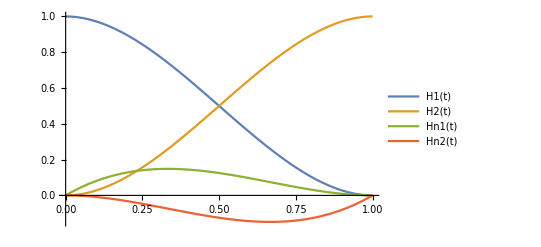

```mathematica
Plot[{H1[t], H2[t], Hn1[t],Hn2[t]},{t,0,1}, PlotLegends->"Expressions"]
```

H1(t) and H2(t) interpolate the values

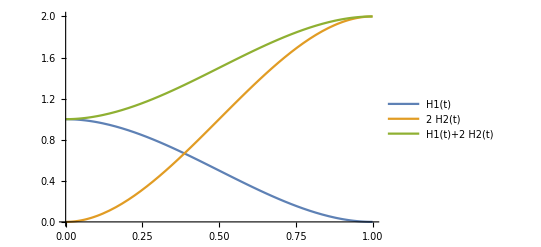

```mathematica
Plot[{H1[t], 2H2[t], H1[t]+2H2[t]},{t,0,1}, PlotLegends->"Expressions"]
```

```mathematica
H1[1]-3H2[1]+1000 Hn1[1]-99.9 Hn2[1]
```

-3.

#### Hn1 (t) and Hn2 (t) interpolate the derivatives

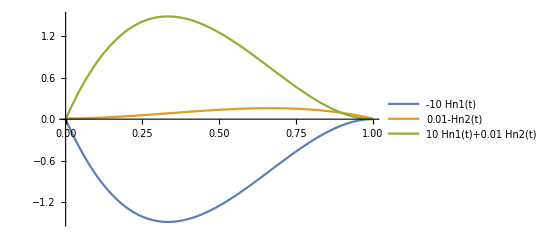

```mathematica
Plot[{-10Hn1[t], 0.01-Hn2[t], 10Hn1[t]+0.01Hn2[t]},{t,0,1}, PlotLegends->"Expressions"]
```

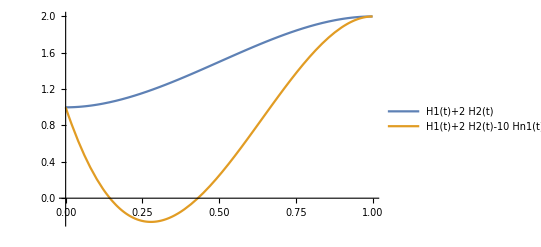

```mathematica
Plot[{ H1[t]+2H2[t],H1[t]+2H2[t]-10Hn1[t]+0.01Hn2[t]},{t,0,1}, PlotLegends->"Expressions"]
```

#### Using the cubic Hermite polynomials for interpolation on the interval [x1, x2] We “translate” and “scale” H1, H2, Hn1, Hn2: x = x1+t (x2-x1)=> t=(x-x1)/(x2-x1) The percentage of (x-x1) in the interval [x2-x1]

```mathematica
x1=2
x2=7
h1=x2-x1
T[x_]:=(x-x1)/h1
```

2

7

5

```mathematica
y1=8 
y2=4
p1 = -1
p2 = 10
```

8

4

-1

10

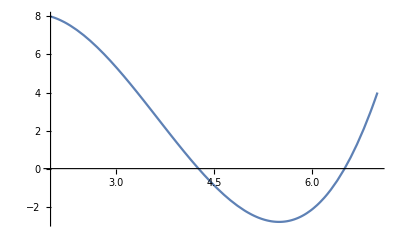

```mathematica
Plot[ y1 H1[T[x]] + y2 H2[T[x]]+p1 *h1 Hn1[T[x]]+ p2*h1  Hn2[T[x]],{x,x1,x2}]
```

More systematically :

```mathematica
T[x_, x1_, x2_]:=(x-x1)/(x2-x1)
```

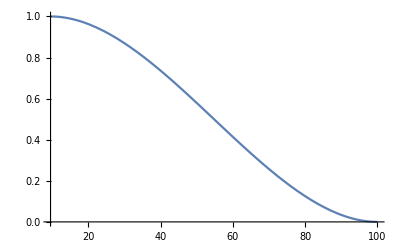

```mathematica
Plot[ H1[T[x, 9.55, 100]], {x, 9.55, 100}]
```